# A Brief Introduction to Mamthematica:

Online resource:
http://www.wolfram.com/support/learn/
http://www.math.harvard.edu/computing/math/tutorial/
http://www.cs.purdue.edu/homes/ayg/CS590C/www/mathematica/math.html

In your notebook, type a piece of code, then press Shift+Enter, Mathematica will run the code and report the results.

```mathematica
2 + 2
102/9
```

4

34/3

The default format is fraction.  You have to explicitly specify numerical approximations by N[...] command
Notice that Mathematica uses square brackets to delimit the argument of a function, instead of the more conventional parentheses.
You can add either text or mathematica input by specifying the new input category.  You can remove anything from the notebook by “cut” it.

```mathematica
N[102 / 9]
N[102/9,20]
```

11.3333

11.333333333333333333

Manipulating Lists by Their Indices:

Note that list index starts at 1, not 0.

Part[list,spec] or list[[spec]]				part or parts of a list
Part[list,spec1,spec2,...] or list[[spec1,spec2,...]]	part or parts of a nested list
n							the n part from the beginning
-n							the n part from the end
{i1,i2,...}						a list of parts
m;;n							parts m through n
All							all parts

```mathematica
a={1,2,3};
Part[a,1]
a[[1]]
```

1

1

Defining Functions:
This defines the function f. Notice the _ on the left-hand side.

```mathematica
f[x_]:=x^2
```

Table[expr, {imax}]
generates a list of imax copies of expr.

Table[expr, {i, imax}]
generates a list of the values of expr when i runs from 1 to imax.

Table[expr, {i, imin, imax}]
starts with i=imin.

Table[expr, {i, imin, imax, di}]
uses steps di.

Table[expr, {i, {i1, i2, ...}}] 
uses the successive values i1, i2, ....

Table[expr, {i, imin, imax}, {j, jmin, jmax}, ...]
gives a nested list. The list associated with i is outermost.

```mathematica
Table[i^2,{i,10}]
Table[f[i], {i,0,20,2}]
Table[10i+j,{i,4},{j,3}]
MatrixForm[%]
```

{1,4,9,16,25,36,49,64,81,100}

{f[0],f[2],f[4],f[6],f[8],f[10],f[12],f[14],f[16],f[18],f[20]}

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33
41 | 42 | 43)

To check the manual of certain command, just type two question marks before it.

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

Attributes[Plot]={HoldAll,Protected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→System`Private`$Evaluated,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Some Coding Examples

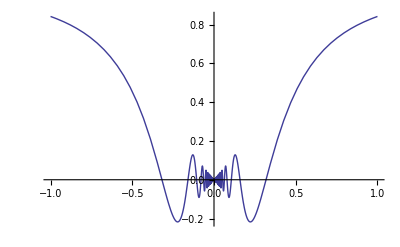

```mathematica
Plot[x*Sin[1/x],{x,-1,1}]
```

```mathematica
Plot3D[Sin[x*y],{x,-3,3},{y,-3,3}];Display["plot3.ps",%,"EPS"]
```

Export::obsalt: Display is obsolete. Instead, use Export.

-Graphics-

```mathematica
Plot3D[Sin[x*y],{x,-3,3},{y,-3,3},PlotPoints->100,Mesh->False,Boxed->False]
```

-Graphics3D-

# Examples on parametric Curves

```mathematica
parabola[t_]:={t, 2t-2t^2, 0.};
pdata=Table[parabola[t], {t,-2,2, 0.01}];
xaxis={{-10,0,0},{10,0,0}};
a1=Graphics3D[{Thick,Green,Dashed, Line[xaxis]}];
yaxis={{0, -10,0},{0, 10,0}};
a2=Graphics3D[{Thick,Red,Dashed, Line[yaxis]}];
zaxis={{0, 0, -10},{0, 0, 10}};
a3=Graphics3D[{Thick,Blue,Dashed, Line[zaxis]}];
poly= Graphics3D[Line[pdata]];
Show[{poly, a1, a2, a3}]
```

-Graphics3D-

```mathematica
parabola[t_]:={-2t+2t^2,t, 0.};
pdata=Table[parabola[t], {t,-2,2, 0.01}];
xaxis={{-10,0,0},{10,0,0}};
a1=Graphics3D[{Thick,Green,Dashed, Line[xaxis]}];
yaxis={{0, -10,0},{0, 10,0}};
a2=Graphics3D[{Thick,Red,Dashed, Line[yaxis]}];
zaxis={{0, 0, -10},{0, 0, 10}};
a3=Graphics3D[{Thick,Blue,Dashed, Line[zaxis]}];
poly= Graphics3D[Line[pdata]];
Show[{poly, a1, a2, a3}]
```

-Graphics3D-

```mathematica
helix[t_]:={10*Cos[t], 10*Sin[t], t}
hdata = Table[helix[t], {t,-10,10,0.02}];
xaxis={{-10,0,0},{10,0,0}};
a1=Graphics3D[{Thick,Green,Dashed, Line[xaxis]}];
yaxis={{0, -10,0},{0, 10,0}};
a2=Graphics3D[{Thick,Red,Dashed, Line[yaxis]}];
zaxis={{0, 0, -10},{0, 0, 10}};
a3=Graphics3D[{Thick,Blue,Dashed, Line[zaxis]}];
poly= Graphics3D[Line[hdata]];
Show[{poly, a1, a2, a3}]
```

-Graphics3D-

# Parametric format of a Bezier Curve

```mathematica
curv[t_]:={-(1-t)^3+t^3, 3(1-t)^2t-3(1-t)t^2, 0};
c=Table[curv[t], {t,0,1,0.02}];
xaxis={{-1,0,0},{1,0,0}};
a1=Graphics3D[{Thick,Red,Dashed, Line[xaxis]}];
yaxis={{0, -1,0},{0, 1,0}};
a2=Graphics3D[{Thick,Green,Dashed, Line[yaxis]}];
zaxis={{0, 0, -1},{0, 0, 1}};
a3=Graphics3D[{Thick,Blue,Dashed, Line[zaxis]}];
poly=Graphics3D[Line[c], Axes->True];
Show[{poly, a1, a2, a3}]
curv[0.5]
```

-Graphics3D-

{0.,0.,0}

```mathematica
dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];
b={{-1, 0, 0}, {0,1,0}, {0, -1,0}, {1, 0,0}};
n=Length[b]-1;
curve=ParametricPlot3D[dca[b,n,0,t],{t,0,1},PlotStyle->{Thick, Orange}];
poly=Graphics3D[{Thick,Yellow,Line[b]}];
points=Graphics3D[{PointSize[Large],Green,Point[b]}];
xaxis={{-2,0,0},{2,0,0}};
a1=Graphics3D[{Thick,Red,Dashed, Line[xaxis]}];
yaxis={{0, -2,0},{0, 2,0}};
a2=Graphics3D[{Thick,Green,Dashed, Line[yaxis]}];
zaxis={{0, 0, -1},{0, 0, 1}};
a3=Graphics3D[{Thick,Blue,Dashed, Line[zaxis]}];
Show[{poly,curve, a1, a2, a3}]
```

-Graphics3D-

# de Casteljau Algorithm

```mathematica
dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];

b={{0,0,0},{1,0,0},{1,0,1},{1,1,1},{1,1,0},{0,1,0}};
n=Length[b]-1;
b[[2]]
c={1,2,3}
c[[1]]
Part[b,1]
```

{1,0,0}

{1,2,3}

1

{0,0,0}

```mathematica
curve=ParametricPlot3D[dca[b,n,0,t],{t,0,1},PlotStyle->{Thick, Green}];
poly=Graphics3D[{Thick,Green,Line[b]}];
points=Graphics3D[{PointSize[Large],Green,Point[b]}];
Show[{poly,curve}]
```

-Graphics3D-

## Nested Polygons

This plost all intermediate line segemtns arising in the de Casteljau algorithm for several values of t.

```mathematica
polyr[b_,r_,t_]:=Table[dca[b,r,i,t],{i,0,n-r}];

nested[b_,t_]:=Graphics3D[Line[Table[polyr[b,r,t] ,{r,0,n}]]];

tree=Table[nested[b,t],{t,0,1,0.02}];


Show[{tree,curve,points,poly}]
```

-Graphics3D-

Rotation invariance

```mathematica
dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];
b={{0, 1, 0}, {1, 0,0}, {-1,0,0}, {0, -1,0}};
n=Length[b]-1;
curve=ParametricPlot3D[dca[b,n,0,t],{t,0,1},PlotStyle->{Thick, Orange}];
poly=Graphics3D[{Thick,Yellow,Line[b]}];
points=Graphics3D[{PointSize[Large],Green,Point[b]}];
xaxis={{-2,0,0},{2,0,0}};
a1=Graphics3D[{Thick,Red,Dashed, Line[xaxis]}];
yaxis={{0, -2,0},{0, 2,0}};
a2=Graphics3D[{Thick,Green,Dashed, Line[yaxis]}];
zaxis={{0, 0, -1},{0, 0, 1}};
a3=Graphics3D[{Thick,Blue,Dashed, Line[zaxis]}];
Show[{poly,curve, a1, a2, a3}]
```

-Graphics3D-